## call packages

1. corr_proj _funcs.m will call pdfParsePDS2013.m and dtareadbotingw2016.m
1a. pdfParsePDS2013.m contains functions of PDF intepolation
1b. dtareadbotingw2016.m contains functions of reading and tackling experimental data sets from .dta files
1c. corr_proj _funcs.m contains all functions needed for making PDF constraint plots, including calculating PDFs, correlations, and sensitivities, drawing plots, and e.t.c.

```mathematica
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ];
Print["present directory: ",Directory[]];
lib1="corr_proj_funcs.m";
If[FileExistsQ[lib1],Print["loading ",lib1];Get[lib1],Print["library file ",lib1," doesn't exist"] ];
(*Get["corr_proj_funcs.m"]*)
Print["present directory: ",Directory[]];
```

present directory: /home/botingw/Downloads/Sean_20171114/PDFsense-master_0228/bin

loading corr_proj_funcs.m

present directory: /home/botingw/Downloads/Sean_20171114/PDFsense-master_0228/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

present directory: /home/botingw/Downloads/Sean_20171114/PDFsense-master_0228/bin

## dtareadbotingw2016.m and corr_proj _funcs.m

```mathematica
?dtaread2016boting`*
```

### functions that get information of specific Expt ID

```mathematica
ExptIDtoName[101]
ExptIDEcm[101]
ExptIDinfo[101]
ExptIDprocess[101]
```

can not find expt id = 101 in lisTable

None

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 101

-1

DIS

{101,{BCDMS,pμ → μX,,}}

```mathematica
ExptIDtoName[201]
ExptIDEcm[201]
ExptIDinfo[201]
ExptIDprocess[201]
```

can not find expt id = 201 in lisTable

None

38.8

VBP2

{201,{E605,𝓅𝒞𝓊 → μ^+μ^-X,,38.8}}

### datalist file reading

```mathematica
datalistFile="dat17lisformathematica";
FileExistsQ[datalistFile]
```

True

1. ReadLisFile read a datalis file and extract expt ID names in the file

```mathematica
ReadLisFile[datalistFile]
```

{{101,BcdF2pCor},{102,BcdF2dCor},{103,NmcF2pCor},{104,NmcRatCor},{105,NmcF2rX},{106,NmcX0pCor},{115,BcdX0pCor},{116,BcdX0dCor},{108,cdhswf2},{109,cdhswf3},{110,ccfrf2.mi},{111,ccfrf3.md},{122,ChorusNuX0},{123,ChorusNbX0},{124,NuTvNuChXN},{125,NuTvNbChXN},{126,CcfrNuChXN},{127,CcfrNbChXN},{140,Hn+9697f2c},{143,Hn+9900x0c},{145,Hn+9900x0b},{146,Hn0407f2c},{147,Hn1X0c},{156,Zn+9697f2c},{157,Zn+9800f2c},{159,HERA1X0},{160,HERAIpII},{164,e140Rd},{165,e143RC},{166,H1FL00},{167,H1FL03a},{168,H1FL03b},{169,H1FL10},{170,EMCF2c},{171,EMCX0c},{180,epFLbench},{181,epF1bench},{182,epF2bench},{183,epF3bench},{184,emFLbench},{185,emF1bench},{186,emF2bench},{187,emF3bench},{201,e605},{203,e866f},{204,e866ppxf},{205,e866pdxf},{221,cdfWprod},{225,cdfLasy},{227,cdfLasy2},{231,d02Easy1},{232,d02Easy2},{233,d02Easy3},{234,d02Masy1},{235,d02Masy2},{236,d02Masy3},{240,LHCb7_WZ1},{241,LHCb7Wasy1},{242,LHCb7Wasy2},{243,LHCb7Wasy3},{244,LHCb7Wa1N},{245,LHCb7ZWrap},{246,LHCb8Zeer},{247,ATL7Zpt},{248,ATL7ZW},{249,CMS8Wxa},{250,LHCb8WZ},{260,ZyD02a},{261,ZyCDF2},{265,CMS7Masy1},{266,CMS7Masy2},{267,CMS7Easy},{268,ATL7_WZ},{275,ATL7DYhm},{276,ATL7DYlm},{277,ATL7DYext},{281,d02Easy5},{283,d02EasyI},{284,d02EasyII},{285,d02EasyIII},{286,d02EasyIV},{299,ATL13_WZ},{401,ttbTeV2},{402,ttbLHC7},{403,ttbLHC8},{404,ttbLHC14},{405,ttbLHC13},{504,cdf2jtCor2},{505,cdf1jtCorB},{506,cdf1jtCorB},{514,d02jtCor2},{515,d01Bjet},{517,d01Bjet},{518,d02dijet},{534,ATL7jtR4},{535,ATL7jtR6},{536,ATL7dijtR4},{537,ATL7dijtR6},{538,CMS7jtR7v2},{542,CMS7jtR7y6},{543,ATL7jtR4u},{544,ATL7jtR6u},{551,ATLratR4},{552,ATLratR6},{561,CMS8ttbpt},{562,CMS8ttbya},{563,CMS8ttbmtt},{564,CMS8ttbytt},{565,ATL8ttbpt},{566,ATL8ttbya},{567,ATL8ttbmtt},{568,ATL8ttbytt},{601,ptE288},{602,ptE605},{603,ptCDFz1},{604,ptD0z1},{605,ptR209},{606,ptD0z2},{607,ptCDFz2},{701,fkH0a7},{702,fkH0a8},{703,fkH0a14},{704,fkWp},{705,fkWm},{706,fkZ0},{707,fkH0a13},{708,fkZ0pr},{709,fkWppr},{710,fkWmpr}}

### functions that get information of specific Expt ID (again)

1. compared with the previous ExptIDtoName who outputs an error message, we find we can get Expt ID names after calling ReadLisFile 

2. some functions in the dtareadbotingw2016.m, like, need Expt ID names, so we recommend users to call ReadLisFile before calling other functions in the dtareadbotingw2016.m

```mathematica
ExptIDtoName[101]
ExptIDEcm[101]
ExptIDinfo[101]
ExptIDprocess[101]
```

BcdF2pCor

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 101

-1

DIS

{101,{BCDMS,pμ → μX,,}}

```mathematica
ExptIDtoName[201]
ExptIDEcm[201]
ExptIDinfo[201]
ExptIDprocess[201]
```

e605

38.8

VBP2

{201,{E605,𝓅𝒞𝓊 → μ^+μ^-X,,38.8}}

### .dta files reading

```mathematica
?Readdtafile*
```

Global`Readdtafile

Readdtafile=<|readdta→readexptsbydta,toclass→todtadataclass|>

steps for reading .dta files
1. set PDF set Directory with .dta files
2. set Expt ID List we want to read
3. call Readdtafile[[“readdta”]]

#### read data from PDF set Directory

```mathematica
DtaDir="../example/CT14NNLO_example/";
```

```mathematica
exptlist={124,225,504};
```

```mathematica
exptdata=Readdtafile[["readdta"]][DtaDir,exptlist]
```

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.00.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.01.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.02.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.03.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.04.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.05.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.06.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.07.dta

42 experiment record(s) read from ../example/CT14NNLO_example/CT14nn.08.dta

find exptid = 124.

find exptid = 225.

find exptid = 504.

{{{124,NuTvNuChXN,     Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2,1.,38,R^2, r(k) =    0.311  -0.558,{dtaread2016boting`Private`LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04],36,dtaread2016boting`Private`LF[10.79,0.326,0.771,0.0354568,0.0373017,0.005713,0.951,0.153,0.104,-0.002082,0.03754,0.005713,0.]},-1.82865,R^2, r(k) =    0.311  -0.558},7,{124,NuTvNuChXN,5,-2.01874,R^2, r(k) =    0.095  -0.309}},{1},{1}}
 |  |  |  |

```mathematica
(*dimensions should be {expt ID, iset, data and information}*)
(*where iset are central set and error sets in each PDF set*)
Dimensions[exptdata]
```

{3,9,9}

```mathematica
(*1~6, 8~9 include information of a data set*)
Take[exptdata[[1,1]],6]
```

{124,NuTvNuChXN,     Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2,1.,38,R^2, r(k) =    0.311  -0.558}

```mathematica
exptdata[[1,1,8]]
exptdata[[1,1,9]]
```

-1.82865

R^2, r(k) =    0.311  -0.558

```mathematica
(*7 is data*)
Take[exptdata[[1,1,7]],3]
```

{dtaread2016boting`Private`LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04],dtaread2016boting`Private`LF[2.994,0.167,0.324,0.0827406,0.0845308,0.009422,0.979,0.111,0.036,-0.004718,0.08746,0.009422,-0.1],dtaread2016boting`Private`LF[4.182,0.326,0.324,0.0373734,0.038635,0.004629,0.967,0.12,0.074,-0.002156,0.03953,0.004629,-0.04]}

after reading .dta files by Readdtafile[[“readdta”]]
we can: 
1. transform .dta data into an association <||> with data and data info by Readdtafile[[“toclass”]]

2. find the (x,Q) specifying PDF that characterize kinematic quantities of the data points (see Samept method in the tutorial) by selectExptxQv2

3. to make data more clear, using Datamethods[[“LFglobal”]] to transform  dtaread2016boting`Private`LF into LF

after doing the three things, 
we can begin to operate transformed data
(Datamethods includes many useful functions for operating these data)

#### transform .dta data into dtadataclass

Readdtafile[[“toclass”]] transform output data of Readdtafile[[“readdta”]]  into an associations structure (<|a->xxx, b->xxx, ...|>)

```mathematica
PDFname=StringSplit[DtaDir,"/"][[-1]]
```

CT14NNLO_example

```mathematica
PDFsetmethod="Hessian"
```

Hessian

```mathematica
exptdataclass=
Table[
Readdtafile[["toclass"]][exptdata[[iexpt,iset]],PDFname,PDFsetmethod],
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
]
```

{{<|label→{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2},3,rawdata→{124,NuTvNuChXN,     Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2,1.,38,R^2, r(k) =    0.311  -0.558,-1.82865,R^2, r(k) =    0.311  -0.558}|>,7,<|label→{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2},3,rawdata→{124,NuTvNuChXN,   …Chi2,1.,38,…,-2.01874,R^2, r(k) =    0.095  -0.309}|>},{1},{1}}
 |  |  |  |

```mathematica
Dimensions[exptdataclass]
```

{3,9}

an association stores PDF info and Expt info of a data set

```mathematica
exptdataclass[[1,1]]//Keys
```

{label,data,exptinfo,PDFinfo,rawdata}

```mathematica
exptdataclass[[1,1]][["exptinfo"]]
```

<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>

```mathematica
exptdataclass[[1,1]][["PDFinfo"]]
```

<|PDFname→CT14NNLO_example,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

the number of a “data” point and it’s “label” should be the same

```mathematica
exptdataclass[[1,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2}

```mathematica
exptdataclass[[1,1]][["label"]]//Length
exptdataclass[[1,1]][["data"]][[1]]//Length
(*# of data points*)
exptdataclass[[1,1]][["data"]]//Length
```

13

13

38

### find the (x,Q) specifying PDF that characterize kinematic quantities of the data points

selectExptxQv2 find the (x,Q) specifying PDF that characterize kinematic quantities of the data points 
it inputs Expt ID and Expt ID data, then output the data with (x,Q) of the points added

```mathematica
exptdataPDFxQclass=
Table[
tmpdata=exptdataclass[[iexpt,iset]];
tmpdata[["data"]]=
selectExptxQv2[tmpdata[["exptinfo","exptid"]],tmpdata[["data"]],"dummy"];
tmpdata[["label"]]=Join[tmpdata[["label"]],{"x","Q"}];
tmpdata,
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
];
```

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 124

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 124

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 124

«6 more identical outputs»

```mathematica
exptdataPDFxQclass//Dimensions
```

{3,9}

comparison of exptdataclass & exptdataPDFxQclass:
{x,Q} are appended to data points of exptdataPDFxQclass
# of points may be changed (CDF lepton asymmetry as an example, there are two (x,Q) points who are the LO contribution of a data point)

```mathematica
exptdataclass[[2,1]][["label"]]
exptdataclass[[2,1]][["data"]][[1]]
```

{Y,Q,Rs,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2}

dtaread2016boting`Private`LF[0.109,80.38,1800.,0.018,0.0215356,0.008001,0.836,0.372,0.195,0.,0.018,0.008001,0.2]

```mathematica
exptdataPDFxQclass[[2,1]][["exptinfo","exptname"]]
```

cdfLasy

```mathematica
exptdataPDFxQclass[[2,1]][["label"]]
exptdataPDFxQclass[[2,1]][["data"]][[1]]
```

{Y,Q,Rs,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

dtaread2016boting`Private`LF[0.109,80.38,1800.,0.018,0.0215356,0.008001,0.836,0.372,0.195,0.,0.018,0.008001,0.2,0.0497982,80.38]

```mathematica
exptdataclass[[2,1]][["exptinfo","exptid"]]
exptdataclass[[2,1]][["data"]]//Length
```

225

11

```mathematica
exptdataPDFxQclass[[2,1]][["exptinfo","exptid"]]
exptdataPDFxQclass[[2,1]][["data"]]//Length
```

225

22

#### transform local defined functions dtaread2016boting`Private`LF back to global functions LF

since dtaread2016boting`Private`LF is not LF,
we use Datamethods[[“LFglobal”]] to transform it into LF

the data structure become:
{LF[a1,a2,...], LF[a1,a2,...], ...}

```mathematica
Take[exptdataPDFxQclass[[1,1]][["data"]],3]
```

{dtaread2016boting`Private`LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04,0.101,2.328],dtaread2016boting`Private`LF[2.994,0.167,0.324,0.0827406,0.0845308,0.009422,0.979,0.111,0.036,-0.004718,0.08746,0.009422,-0.1,0.167,2.994],dtaread2016boting`Private`LF[4.182,0.326,0.324,0.0373734,0.038635,0.004629,0.967,0.12,0.074,-0.002156,0.03953,0.004629,-0.04,0.326,4.182]}

```mathematica
exptdataPDFxQclass=
Table[
Datamethods[["LFglobal"]][exptdataPDFxQclass[[iexpt,iset]] ],
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
];
```

```mathematica
(*or we can run /. to replace dtaread2016boting`Private`LF by LF*)
(*
Table[
exptdataclass[[iexpt,iset]][["data"]]=exptdataclass[[iexpt,iset]][["data"]]/.dtaread2016boting`Private`LF:>LF,
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
];
*)
```

```mathematica
Take[exptdataPDFxQclass[[1,1]][["data"]],3]
```

{LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04,0.101,2.328],LF[2.994,0.167,0.324,0.0827406,0.0845308,0.009422,0.979,0.111,0.036,-0.004718,0.08746,0.009422,-0.1,0.167,2.994],LF[4.182,0.326,0.324,0.0373734,0.038635,0.004629,0.967,0.12,0.074,-0.002156,0.03953,0.004629,-0.04,0.326,4.182]}

### some operations of data

1. extract (x,Q) of the data

```mathematica
exptdataPDFxQclass[[1,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
exptdataPDFxQclass[[1,1]][["data"]]/.LF[a__]:>LF@@Take[{a},-2]
```

{LF[0.101,2.328],LF[0.167,2.994],LF[0.326,4.182],LF[0.057,2.295],LF[0.101,3.055],LF[0.167,3.928],LF[0.326,5.489],LF[0.057,2.698],LF[0.101,3.592],LF[0.167,4.618],LF[0.326,6.452],LF[0.057,2.457],LF[0.101,3.271],LF[0.167,4.206],LF[0.326,5.877],LF[0.057,3.225],LF[0.101,4.293],LF[0.167,5.52],LF[0.326,7.712],LF[0.021,2.301],LF[0.057,3.791],LF[0.101,5.046],LF[0.167,6.488],LF[0.326,9.065],LF[0.057,2.925],LF[0.101,3.894],LF[0.167,5.007],LF[0.326,6.996],LF[0.021,2.33],LF[0.057,3.839],LF[0.101,5.11],LF[0.167,6.571],LF[0.326,9.181],LF[0.021,2.739],LF[0.057,4.512],LF[0.101,6.007],LF[0.167,7.724],LF[0.326,10.79]}

2. Expt error ratio

```mathematica
exptdataPDFxQclass[[1,1]][["data"]]/.LF[a__]:>LF[{a}[[6]]/{a}[[4]] ]
```

{LF[0.123077],LF[0.113874],LF[0.123858],LF[0.100007],LF[0.0999652],LF[0.100094],LF[0.110615],LF[0.0965188],LF[0.106374],LF[0.118621],LF[0.130294],LF[0.104641],LF[0.0958001],LF[0.0989567],LF[0.107182],LF[0.098301],LF[0.100947],LF[0.102872],LF[0.118939],LF[0.0952787],LF[0.0903334],LF[0.100485],LF[0.11441],LF[0.132874],LF[0.108059],LF[0.102769],LF[0.102525],LF[0.115866],LF[0.117615],LF[0.115806],LF[0.112213],LF[0.116658],LF[0.131031],LF[0.119099],LF[0.103225],LF[0.102362],LF[0.130126],LF[0.161126]}

3. using functions defined in Datamethods:
functions in Datamethods can deal with the data (data format is the output of Readdtafile[[“toclass”]])

```mathematica
Datamethods//Keys
```

{getdatainfo,getdata,setdata,getNpt,getNcolumn,getdatalabel,add,pick,take,delete,tolist,picktolist,LFglobal}

```mathematica
Datamethods[["getdatainfo"]][exptdataPDFxQclass[[1,1]] ]
```

label:
{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

exptinfo:
<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>

PDFinfo:
<|PDFname→CT14NNLO_example,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

rawdata:
{124,NuTvNuChXN,     Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2,1.,38,R^2, r(k) =    0.311  -0.558,-1.82865,R^2, r(k) =    0.311  -0.558}

{Null,Null,Null,Null,Null}

```mathematica
(*# points and # of labels in the selected expt data*)
Datamethods[["getNpt"]][exptdataPDFxQclass[[1,1]] ]
exptdataPDFxQclass[[1,1]][["data"]]//Length

Datamethods[["getNcolumn"]][exptdataPDFxQclass[[1,1]] ]
exptdataPDFxQclass[[1,1]][["data"]][[1]]//Length
```

38

38

15

15

```mathematica
Datamethods[["getdatalabel"]][exptdataPDFxQclass[[1,1]] ]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*"add","pick","take","delete","tolist","picktolist","LFglobal" are operations of data*)
```

```mathematica
(*add: if the added # of data is not the same as original data, error *)
dataadd=Table[LF[0.1,0.2,0.3],{ipt,10}];
labeladd={"add1","add2","add3"};
Datamethods[["add"]][exptdataPDFxQclass[[1,1]],dataadd,labeladd]
```

error, #points of data & added data are different

$Aborted

```mathematica
(*new data labels and data are appended to the original data*)
dataadd=Table[LF[0.1,0.2,0.3],{ipt,38}];
labeladd={"add1","add2","add3"};
Datamethods[["add"]][exptdataPDFxQclass[[1,1]],dataadd,labeladd][["data"]][[1]]
Datamethods[["add"]][exptdataPDFxQclass[[1,1]],dataadd,labeladd][["label"]]
```

LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04,0.101,2.328,0.1,0.2,0.3]

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,add1,add2,add3}

```mathematica
(*pick: pick specific columns in data points*)
exptdataPDFxQclass[[1,1]][["label"]] 
Datamethods[["pick"]][exptdataPDFxQclass[[1,1]],{1,3,5} ][["label"]]
Datamethods[["pick"]][exptdataPDFxQclass[[1,1]],{1,3,5} ][["data"]][[1]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Q,y,Th./Norm}

LF[2.328,0.324,0.116384]

```mathematica
(*take, delete: Take, Delete function apply on data*)
exptdataPDFxQclass[[1,1]][["label"]] 
Datamethods[["take"]][exptdataPDFxQclass[[1,1]],2 ][["label"]]
Datamethods[["take"]][exptdataPDFxQclass[[1,1]],2 ][["data"]][[1]]

Datamethods[["delete"]][exptdataPDFxQclass[[1,1]],2 ][["label"]]
Datamethods[["delete"]][exptdataPDFxQclass[[1,1]],2 ][["data"]][[1]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Q,x}

LF[2.328,0.101]

{Q,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

LF[2.328,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04,0.101,2.328]

```mathematica
Datamethods[["getNpt"]][exptdataPDFxQclass[[1,1]] ]
Datamethods[["getNcolumn"]][exptdataPDFxQclass[[1,1]] ]
exptdataPDFxQclass[[1,1]][["data"]][[1]]
exptdataPDFxQclass[[1,1]][["data"]]//Dimensions

(*LF->List for all data points*)
Datamethods[["tolist"]][exptdataPDFxQclass[[1,1]] ]//Dimensions
(*pick 1, 3, 5 columns for each data point, then LF->List*)
Datamethods[["picktolist"]][exptdataPDFxQclass[[1,1]],{1,3,5} ]//Dimensions
```

38

15

LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04,0.101,2.328]

{38}

{38,15}

{3,38}

## pdfParsePDS2013.m

```mathematica
(*show functions under pdfParsePDS2013.m*)
?parsePDS`*
```

### initialize the PDF set

```mathematica
myPDFsetDir="../example/CT14NNLO_example/"
```

../example/CT14NNLO_example/

```mathematica
(*setup pdf function*)
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ[myPDFsetDir<>"*pds",ifamily];
```

Included 0 more files in the PDF family 1

Included 9 more files in the PDF family 1

### intepolating the PDF values

#### for single point

```mathematica
(*intepolating PDF values for all error sets*)
x=0.01;Q=1.3;gluon=0;
gxQlowQ=pdfCTEQFamily[x,Q,gluon]
```

{161.089,162.423,159.952,161.138,162.678,176.587,169.691,165.104,165.845}

```mathematica
x=0.01;Q=10.0;gluon=0;
gxQmediumQ=pdfCTEQFamily[x,Q,gluon]
```

{644.161,642.468,643.284,640.861,646.543,637.057,656.99,649.348,638.251}

```mathematica
x=0.01;Q=100.0;gluon=0;
gxQhighQ=pdfCTEQFamily[x,Q,gluon]
```

{799.838,798.053,799.254,796.891,800.91,789.549,806.884,802.414,794.065}

#### for many inputted points in {LF[x,Q],LF[x,Q],...}

```mathematica
Directory[]
```

/home/botingw/Downloads/Sean_20171114/PDFsense-master_0228/bin

```mathematica
Pdsread//Keys
```

{fxQ,fxQsamept}

```mathematica
(*Pdsread[["fxQ"]] could build a data with inputted info (PDF set, flavour,...) and PDFs of all (x,Q) values and all sets*)
myPDFsetDir="../example/CT14NNLO_example/";
PDFsetmethod="Hessian";
gluon=0;
xQLF=Table[LF[10^ix,10^iQ],{ix,-3,-1},{iQ,1,3}]//Flatten;

gxQLF=Pdsread[["fxQ"]][xQLF,myPDFsetDir,PDFsetmethod,gluon];
```

Included 0 more files in the PDF family 1

Included 9 more files in the PDF family 1

```mathematica
Datamethods[["getdatainfo"]][gxQLF]
```

label:
{x,Q,0,1,2,3,4,5,6,7,8}

PDFinfo:
<|PDFname→CT14NNLO_example,PDFsetmethod→Hessian,Nset→9,iset→unset,flavour→0|>

{Null,Null,Null}

```mathematica
Datamethods[["getNpt"]][gxQLF]
Datamethods[["getNcolumn"]][gxQLF]
```

9

11

#### for many inputted points in a data

```mathematica
exptdataPDFxQclass[[1,1]][["exptinfo"]]
```

<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>

```mathematica
(**)

exptdataPDFxQclass[[1,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*"fxQsamept" is used to calculate PDFs at (x,Q) which characterize kinematical quantities of data points*)
(*Pdsread[["fxQsamept"]]'s input is only replacing inputs of Pdsread[["fxQ"]]'s {LF[x,Q],LF[x,Q],...} by an Expt data which has the same data structure {LF[x,Q],LF[x,Q],...}*)

gxQExptData=Pdsread[["fxQsamept"]][Datamethods[["take"]][exptdataPDFxQclass[[1,1]],-2],myPDFsetDir,PDFsetmethod,gluon];
```

Included 0 more files in the PDF family 1

Included 9 more files in the PDF family 1

```mathematica
(*compare the difference between results of "fxQ" & "fxQsamept"*)
(*since input of "fxQsamept" is a data with expt info,
the output of "fxQsamept" also includes expt info of the data *)
Datamethods[["getdatainfo"]][gxQExptData]
```

label:
{x,Q,0,1,2,3,4,5,6,7,8}

PDFinfo:
<|PDFname→CT14NNLO_example,PDFsetmethod→Hessian,Nset→9,iset→unset,flavour→0|>

exptinfo:
<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>

{Null,Null,Null,Null}

```mathematica
Datamethods[["getNpt"]][gxQExptData]
Datamethods[["getNcolumn"]][gxQExptData]
```

38

11

### Hessian correlations the PDF values

#### correlations of any two Lists

```mathematica
(*pdfHessianCorrelation could be only used for the initialized PDFsets (PDFparse package), the #replica should be the same as the initialized PDFset,
so please use pdfHessianCorrelationfake, which could be applied to any length of vectors*)
pdfHessianCorrelation[{1,2,3,4,5,6,7,1,1},{1,2,3,4,5,5,5,2,2}]
pdfHessianCorrelationfake[{1,2,3,4,5,6,7,1,1},{1,2,3,4,5,5,5,2,2}]
```

√(2/3)

√(2/3)

```mathematica
gxQlowQ
gxQmediumQ
pdfHessianCorrelationfake[gxQlowQ,gxQlowQ]
```

{161.089,162.423,159.952,161.138,162.678,176.587,169.691,165.104,165.845}

{644.161,642.468,643.284,640.861,646.543,637.057,656.99,649.348,638.251}

1.

```mathematica
(*show correlation of gluon PDF at various scale*)
pdfHessianCorrelationfake[gxQlowQ,gxQmediumQ]
pdfHessianCorrelationfake[gxQlowQ,gxQhighQ]
pdfHessianCorrelationfake[gxQmediumQ,gxQhighQ]
```

-0.785127

-0.82695

0.99727

#### correlations of PDF uncertainties and observable uncertainties by Samept method (in the tutorial) an example of Corr(g(x,Q), R), R represents the residual of a data point

1. to calculate correlations of PDF uncertainties at (x, Q) and observable uncertainties (by Samept method), we need to run corrfxQresiduesamept[[“corrsamept”]],
which input a dtadata class with data=={LF[x,Q,obs1,obs2,...obsNset],...}
and a fxQsameptdata class with data=={LF[x,Q,f(x,Q,flavour,iset1),...,f(x,Q,flavour,Nset)],...},
two inputted data should have the same # of points

output data with {LF[x, Q, corr], LF[x, Q, corr],...}

2. more flexible way to calculate correlations of two data, users can search the function 
corrAB in corr_proj_func.m

3. users need to build data=={LF[x,Q,obs1,obs2,...obsNset],...} &
{LF[x,Q,f(x,Q,flavour,iset1),...,f(x,Q,flavour,Nset)],...}

we can use following methods to prepare data we need 
a. use Datamethods[[“take”]] to take {x,Q} parts of data
b. use getNsetLF to extract observables of Nset
c. combine {x,Q} and {obs(1),obs(2),...,obs(Nset)} by Datamethods[[“add”]]
d. use Pdsread[[“fxQsamept”]] to calculate Nset PDF values for inputted (x,Q) points

```mathematica
corrfxQresiduesamept//Keys
```

{corrsamept,dRcorrsamept,deltaR,residue}

```mathematica
exptdataPDFxQclass[[1,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*input the dataclass[[Nset]] and the columnN, extract {LF[columnN(1),...,columnN(Nset)]} *)
getNsetLF[dataclassin_,columnin_]:=
Module[{dataclass=dataclassin,column=columnin,dataNset,Nset},
Nset=Length[dataclass];
(*extract Nset of data [[iset,{residual},Npt]]*)
dataNset=
Table[
(*grab residual*)
Datamethods[["picktolist"]][dataclass[[iset]],{column} ],
{iset,1,Nset}
];

(*transf to [[Npt,{residual},Nset]] format*)
dataNset=Transpose[dataNset,{3,2,1}];


(*transf to [[Npt,Nset]] format*)
(*CT14NNLO: [[Npt]]=LF[obs0,...obs56]*)
dataNset=
Table[
(*1 represent residual index*)
dataNset[[ix,1]]/.List->LF,
{ix,1,Length[dataNset]}
];

dataNset
]
```

```mathematica
exptdataPDFxQclass[[1,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*get (x,Q) of data points*)
ExptxQ=Datamethods[["take"]][exptdataPDFxQclass[[1,1]],-2];
ExptxQ[["label"]]
```

{x,Q}

```mathematica
(*get Nset of gluon(x,Q) for each (x,Q) point*)
gxQExptData=Pdsread[["fxQsamept"]][ExptxQ,myPDFsetDir,PDFsetmethod,gluon];
```

Included 0 more files in the PDF family 1

Included 9 more files in the PDF family 1

```mathematica
gxQExptData[["label"]]
```

{x,Q,0,1,2,3,4,5,6,7,8}

```mathematica
(*get residual (Th-ShiftedData/UnCorrError) of Nset *)
(*this function append (label[[5]]-label[[12]])/label[[13]] to each data point, which assumes 5, 12, 13 are Th, ShiftedData, UnCorrError*)
ExptResidual=
Table[
addresidue[exptdataPDFxQclass[[1,iset]] ],{iset,1,Dimensions[exptdataPDFxQclass][[2]]}
];
```

```mathematica
(*another way to add residuals to data points:

ThIndex=5;ShiftDatIndex=11;UnCorrErrIndex=12;

ExptResidual=
Table[
tmpExptData=exptdataPDFxQclass[[1,iset]];
tmpExptData[["data"]]=tmpExptData[["data"]]/.LF[a__]:>LF[Sequence@@{a},({a}[[ThIndex]]-{a}[[ShiftDatIndex]])/{a}[[UnCorrErrIndex]] ];
tmpExptData[["label"]]=Join[tmpExptData[["label"]],{"residual"}];
"dummy",
{iset,1,Dimensions[mydtadata][[2]]}
];

*)
```

```mathematica
ExptResidual[[1]][["label"]]
ExptResidual[[1]][["data"]][[1]]
Datamethods[["getNpt"]][ExptResidual[[1]] ]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,residual}

LF[2.328,0.101,0.324,0.107412,0.116384,0.01322,0.923,0.114,0.461,-0.006495,0.1139,0.01322,0.04,0.101,2.328,0.187897]

38

```mathematica
(*getNsetLF input dataclass[[Nset]] and the n-th column*)
(*output the extracted for each data point{LF[n(1),n(2),...n(Nset)],LF[n(1),n(2),...n(Nset)],...}*)
residualNsetLF=getNsetLF[ExptResidual,-1];
```

```mathematica
residualNsetLF//Dimensions
residualNsetLF[[1]]
```

{38}

LF[0.187897,0.128744,0.19531,0.217247,0.144024,0.150454,0.271256,0.252345,0.103782]

```mathematica
ExptxQ[["data"]]//Length
ExptxQ[["label"]]
residualNsetLF//Length
```

38

{x,Q}

38

```mathematica
(*append residuals of Nset to (x,Q) of each data point*)
Nset=Dimensions[ExptResidual][[1]]
residualNsetclass=Datamethods[["add"]][ExptxQ,residualNsetLF,Table[ToString[iset],{iset,1,Nset}] ];
```

9

```mathematica
residualNsetclass[["label"]]
residualNsetclass[["data"]][[1]]
```

{x,Q,1,2,3,4,5,6,7,8,9}

LF[0.101,2.328,0.187897,0.128744,0.19531,0.217247,0.144024,0.150454,0.271256,0.252345,0.103782]

```mathematica
corrfxQresiduesamept//Keys
```

{corrsamept,dRcorrsamept,deltaR,residue}

```mathematica
residualNsetclass//Length
gxQExptData//Length
residualNsetclass[["data"]][[1]]
gxQExptData[["data"]][[1]]
```

5

4

LF[0.101,2.328,0.187897,0.128744,0.19531,0.217247,0.144024,0.150454,0.271256,0.252345,0.103782]

LF[0.101,2.328,13.1405,13.1672,13.1057,13.1893,12.9362,12.858,12.4637,12.7922,13.2221]

```mathematica
(*input g(x,Q) and residual of Nset Expt data*)
(*output corr(g(x,Q),R), dR*corr(g(x,Q),R), dR data*)
CorrfxQResidualData=corrfxQresiduesamept[["corrsamept"]][residualNsetclass,gxQExptData];
dRCorrfxQResidualData=corrfxQresiduesamept[["dRcorrsamept"]][residualNsetclass,gxQExptData];
dRResidualData=getdeltaRclass[residualNsetclass];
```

```mathematica
CorrfxQResidualData[["label"]]
dRCorrfxQResidualData[["label"]]
dRResidualData[["label"]]
```

{x,Q,corr}

{x,Q,corr}

{x,Q,deltaR}

```mathematica
(*check dR*corr(g(x,Q),R)=dR*corr(g(x,Q),R)*)
dRCorrfxQResidualData[["data"]][[1,3]]
CorrfxQResidualData[["data"]][[1,3]]*dRResidualData[["data"]][[1,3]]
```

-0.0759696

-0.0759696

## drawing figures

1. note: all plotting functions eat data structure = {LF1[...],LF1[...]}, so when input data, remember to replace LF[...] by LF1[...] (ex: data/.LF->LF1)

### 2D-xQ plot: PDFCorrelationplot8 inputs {data1,data2,...} dataN={LF1[obs1,obs2,obs3], LF1[obs1,obs2,obs3],...} data will be plotted on obs1-obs2 plane, with points on (obs1,obs2) and point colors and sizes depend on obs3 and barseperator barseperator is List of numbers which are seperators of different colors

```mathematica
(*here shows examples of drawing figures*)
(*we take correlation calculated previously as input data of figures*)
```

```mathematica
title="";
xtitle="";
ytitle="";
plotrange={0.00001,1,1.0,2000.0}(*GeV*)
stretchx=1;stretchy=1;
barseperator={-0.85,-0.7,-0.5,0.5,0.7,0.85}
```

{0.00001,1,1.,2000.}

{-0.85,-0.7,-0.5,0.5,0.7,0.85}

```mathematica
(*setup for arguments*)
title="title";
xtitle="x";
ytitle="μ [GeV]";
plotrange={0.00001,1,1,1200};
stretchx=1;stretchy=1;
barseperator={-1,-0.2,-0.1,-0.05,0.05,0.1,0.2,1};
legendlabel="";
epilogtext={};
highlightrange={{-100,-0.2},{0.2,100}};
unhighlightsize=0.0075;
```

```mathematica
(*set up color palette*)
barlegend=Set2DxqBarLegend[barseperator,legendlabel(*,highlightrangein_*)]
```

```mathematica
(*with no highlight*)
{PDFCorrelationplot8[{CorrfxQResidualData[["data"]]/.LF->LF1},"No Highlight title",xtitle,ytitle,plotrange,stretchx,stretchy,barlegend,epilogtext,{{0.0,0.0}},unhighlightsize],
(*with highlight*)
PDFCorrelationplot8[{CorrfxQResidualData[["data"]]/.LF->LF1},title,xtitle,ytitle,plotrange,stretchx,stretchy,barlegend,epilogtext,highlightrange,unhighlightsize]}
```

{-Graphics-,-Graphics-}

### histogram of obs3 in data {LF1[obs1,obs2,obs3], LF1[obs1,obs2,obs3],...}

```mathematica
(*data*)
CorrfxQResidualData[["data"]]/.LF[a__]:>{a}[[3]]
```

{-0.704931,-0.333339,0.0263579,0.287178,-0.51073,-0.438749,0.145616,0.330728,-0.435583,-0.466131,0.249282,0.110859,-0.412734,-0.31909,0.1416,0.191214,-0.257189,-0.27959,0.349684,0.0605031,0.292438,-0.199552,-0.290618,0.514709,0.0698245,-0.206148,-0.235203,0.245458,0.0941691,0.174771,-0.101639,-0.150845,0.516094,0.321133,0.278684,-0.0837388,-0.130335,0.628172}

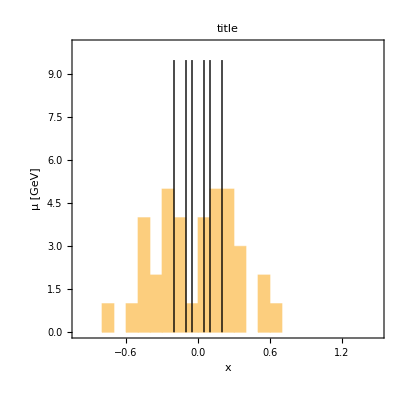

```mathematica
binset={-1,-0.2,-0.1,-0.05,0,0.05,0.1,0.2,1};
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};


(*histogram*)
histplotrange={-1,1.5,0,10};
yrange=histplotrange[[3;;4]];
BinWidth=0.1;
(*set lines on histogram*)
standardlines=setxlineinplot2[CorrfxQResidualData[["data"]]/.LF[a__]:>{a}[[3]],lineelement,yrange];
epilogtext={standardlines};


(*histplot4[CorrfxQResidualData[["data"]]/.LF[a__]:>{a}[[3]],title,xtitle,ytitle,binset,lineelement,histplotrange,Nbin]*)
histplot5[CorrfxQResidualData[["data"]]/.LF[a__]:>{a}[[3]],title,xtitle,ytitle,histplotrange,BinWidth,epilogtext]
```

### (x, Q) distribution of Expt data

```mathematica
(*PDFloglogplot*)
(*expttype could be single, multi, All, ProtonNeutron*)
(*inputs of PDFloglogplot are a little bit tricky*)
(*to make input title, legend,... fancy,
users can run setplotsetting to get input arguments of PDFloglogplot  *)
expttype="single";
plottype=1;
exptlist={CorrfxQResidualData[["exptinfo","exptid"]]};
myplotsetting=setplotsetting[{{CorrfxQResidualData}},exptlist,expttype,plottype,"dummy","dummy"];
imgsize=myplotsetting[["imgsize"]]
title=myplotsetting[["title"]]
xtitle=myplotsetting[["xtitle"]]
ytitle=myplotsetting[["ytitle"]]
lgdlabel=myplotsetting[["lgdlabel"]]
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]]
myMarker=myplotsetting[["marker"]]

lgdpos={0.25,0.725};
xyrangeplot1={xrange,yrange}//Flatten;(*20170307 change it's name, avoid duplicate*)
```

{{700},{700}}

Experimental data in CT14NNLO_example analysis 
  (NuTvNuChXN)

x

μ [GeV]

{NuTvNuChXN}

{RGBColor[0.6, 0.2, 0.],RGBColor[0.2, 0.2, 0.2],RGBColor[1., 0., 0.],RGBColor[1., 0., 0.8],RGBColor[1., 0.6, 0.],RGBColor[0., 0.6, 0.8],RGBColor[0., 0.8, 1.],RGBColor[0.2, 0., 1.],RGBColor[0., 1., 0.4]}

{{▲,5.6},{×,8.4},{△,10.5},{×,8.4},{▲,5.6},{▲,5.6},{×,8.4},{▲,5.6},{▲,5.6}}

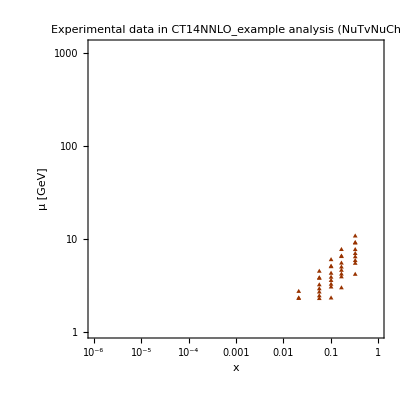

```mathematica
PDFloglogplot[{CorrfxQResidualData[["data"]]/.LF[a__]:>LF1[{a}[[1]],{a}[[2]] ]},myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize]
```

### the function make output figures easier: processdataplotsmultiexp6percentage is a function,

1. processdataplotsmultiexp6percentage is a function that input data of types defined in “config1.txt”
(1:data plots,2:expt error,3:residual,4:”residual error” deltaR_i,5:”sensitivity factor” deltaR_i*Corr(r_i,F),6:”correlation” Corr(r_i,F) ) and flavour index,
output 2D-xQ, histogram, and (x, Q) distribution of the data with title, plot range, and etc be automatically set up

2. the function is defined specifically for plotting data type defined in “config1.txt” 

3. input are data, output of readcorrconfigfile4 (reading configure function), plot type index, flavour index

```mathematica
(*example of reading this funcion*)
```

```mathematica
FileExistsQ["../quick_data/fxQNset_samept_data_CT14NNLO_example.dat"]
FileExistsQ["../quick_data/residualNset_samept_data_CT14NNLO_example.dat"]
```

True

True

```mathematica
ExamplePDFData=Get["../quick_data/fxQNset_samept_data_CT14NNLO_example.dat"];
ExampleResidualData=Get["../quick_data/residualNset_samept_data_CT14NNLO_example.dat"];
```

```mathematica
ExamplePDFData//Dimensions
ExampleResidualData//Dimensions
```

{34,11}

{34}

```mathematica
gluon=0
```

0

```mathematica
(*correlation of all*)
ExampleCorr=
Table[corrfxQresiduesamept[["corrsamept"]][ExampleResidualData[[iexpt]],ExamplePDFData[[iexpt,iflavour+6]] ],{iexpt,Length[ExampleResidualData]},{iflavour,-5,5}];
```

```mathematica
configarguments=readcorrconfigfile6["../example/","config1.txt"]
```

{CT14NNLO_example_ExptInCT14Fit, CT14NNLO_example for showing how to set up configure files ,CT14NNLO_example,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,160,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,248,542,544,249,250,565,566,567,568,545},{0,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,user},{0,0,0,1,0,1,0,0,0,0,1,1},{auto,auto},{1.,6000.},{auto,auto},100,tiny,{1,2,3,4,5,6,7},{0,0,0,0,1,1,0},{{{0.,0.}},{{0.,0.}},{{2.,1000.}},{{0.,0.}},{{-5.,-0.25},{0.25,5.}},{{-1.,-0.7},{0.7,1.}},{{0.,0.}}},{{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}}}}

```mathematica
(*plottype number represent the observable of "# Figures to plot" in config1.txt*)
(*e.g. 6 is correlation*)
(*select the flavour index you want to plot, bbar~b = -5~5*)
plottype=6;flavour=0;
```

```mathematica
(*this function will use a global variable*)
ClassifyMode="single";
```

```mathematica
ExampleCorr//Dimensions
```

{34,11}

can not find expt id = 101 in lisTable

can not find expt id = 102 in lisTable

can not find expt id = 104 in lisTable

can not find expt id = 101 in lisTable

can not find expt id = 102 in lisTable

can not find expt id = 104 in lisTable

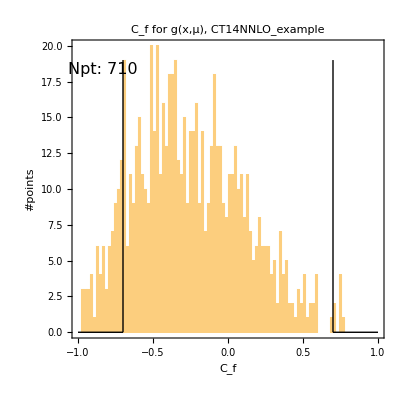
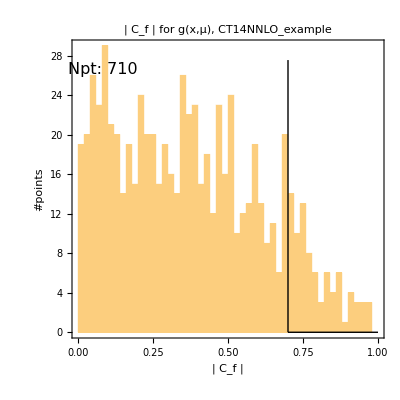
{{-Graphics-,| C_f | for g(x,μ), CT14NNLO_example

 |  | 
Data Sets |  | 
●None(101) | ■None(102) | ◆None(104)
 |  | 
 |  | },{-Graphics-,-Graphics-}}

```mathematica
(*only plot the first 3 experiments*)
processdataplotsmultiexp7percentage[{Take[ExampleCorr,3]},configarguments,plottype,flavour]
```

## Configure files reading

following are examples of reading configure files

### 1. for executable files that make data (ex: fxQsamept_corr.nb)

```mathematica
(*set input arguments *)

configDir="../example/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
(*configfilename="config_pdf_resolution_test.txt";*)
configfilename="../example/savedata_config.txt";
```

```mathematica
(*read arguments from config file*)
{PDFsetDir,PDFsetmethod,ExptIDList,datalistFile,(*FxQGridDir*)dummy2,(*FxQGridFile*)dummy3,FxQSameptDir,FxQSameptFile,CorrDataDir,CorrDataFile,(*GridNx*)dummy6,(*GridNQ*)dummy7}=
readsavedataconfigfile[configDir,configfilename]
```

{../example/CT14NNLO_example/,Hessian,{101,102,104,106,108,109,110,111,124,125,126,127,145,147,159,169,201,203,204,225,227,234,240,241,260,261,266,267,268,281,504,514,535,538},dat170928lisformathematica,default,default,default,default,default,default,10,5}

### 2. for executable files that draw figures by data

```mathematica
(*set config file path*)
configDir="../example/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
configfilename="config1.txt";

(*20170301: new config file
{runfunc,figureDir,dummy1,dummy2,PDFname,dummy3,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
*)
(*new config file*)
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,(*Hist1figureYrange*)dummy12,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=
readcorrconfigfile6[configDir,configfilename]
```

{CT14NNLO_example_ExptInCT14Fit, CT14NNLO_example for showing how to set up configure files ,CT14NNLO_example,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,160,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,248,542,544,249,250,565,566,567,568,545},{0,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,user},{0,0,0,1,0,1,0,0,0,0,1,1},{auto,auto},{1.,6000.},{auto,auto},100,tiny,{1,2,3,4,5,6,7},{0,0,0,0,1,1,0},{{{0.,0.}},{{0.,0.}},{{2.,1000.}},{{0.,0.}},{{-5.,-0.25},{0.25,5.}},{{-1.,-0.7},{0.7,1.}},{{0.,0.}}},{{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}}}}

### 3. for IO filenames setting in drawing plots executable files

```mathematica
plotdataconfigfilename="plotdata_config.txt";
{datalistFile,(*FxQGridDir*)dummy1,(*FxQGridFile*)dummy2,(*FxQSameptDir*)dummy3,(*FxQSameptFile*)dummy4,CorrDataDir,CorrDataFile,(*GridNx*)dummy5,(*GridNQ*)dummy6}=
readplotdataconfigfile[configDir,plotdataconfigfilename]
```

{dat170928lisformathematica,default,default,default,default,default,default,10,5}